```mathematica
norm[s_, x_]:= Exp[-(x/s)^2/2]/(s Sqrt[2 Pi]);
lapl[b_, x_]:= Exp[-Abs[x/b]]/(2 b);
```

```mathematica
poslapl[b_, x_]:= Exp[-x/b]/(2 b);
```

```mathematica
Integrate[norm[s, t] 10^t, t]
```

(∫2^(-1/2+t) 5^t ⅇ^(-t^2/(2 s^2))ⅆt)/(√π s)

```mathematica
Integrate[poslapl, t]
```

```mathematica
Integrate[lapl[.1, t] 10^t, {t, -Infinity, Infinity}]
```

1.05599

```mathematica
NIntegrate[lapl[.1, t] 10^t, {t, -Infinity, Infinity}]
```

1.05599

```mathematica
Integrate[poslapl[b, -t] 10^t, t]
```

(10^t ⅇ^(t/b))/(2+b Log[100])

(10^t ⅇ^(-t/b))/(-2+b Log[100])

```mathematica
Integrate[lapl[b, t] 10^t, t]
```

(∫2^(-1+t) 5^t ⅇ^(-Abs[t/b])ⅆt)/b

```mathematica
Simplify[D[(10^t ⅇ^(-t/b))/(2(b Log[10]-1)), t]]
```

(2^(-1+t) 5^t ⅇ^(-t/b))/b

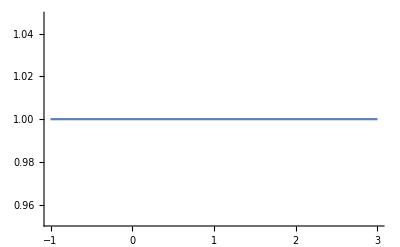

```mathematica
Plot[Exp[x]/(10^(x/Log[10])), {x, -1, 3}]
```

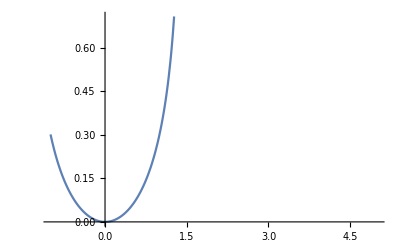

```mathematica
Plot[Log10[1/(1 - s^2/2)], {s, -1, 5}]
```

```mathematica
Table[Log[10] - Sqrt[2]/s, {s, 0.1, 1, .1}]
```

{-11.8396,-4.76848,-2.41146,-1.23295,-0.525842,-0.0544375,0.28228,0.534818,0.731237,0.888372}

```mathematica
N[Sqrt[2]/Log[10]]
```

0.614185

```mathematica
Simplify[(2*(b + 1))^(-1) -(2*(b - 1))^(-1) ]
```

1/(1-b^2)

```mathematica
Simplify[1/(1-(s^2/2))]
```

-2/(-2+s^2)

```mathematica
Simplify[(2*(b + 2))^(-1) -(2*(b - 2))^(-1) ]
```

-2/(-4+b^2)

```mathematica
Simplify[-2/(-4+(s^2/2)^2)]
```

-8/(-16+s^4)

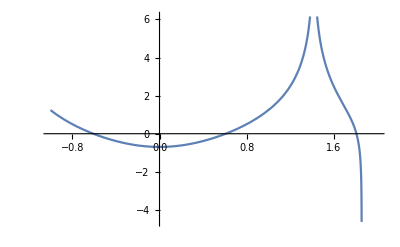

```mathematica
Plot[Log[(-2/(-2+s^2))^2+8/(-16+s^4) ], {s, -1, 2}]
```

```mathematica
s = 1;
m = .1;
pts = Table[NIntegrate[10^t Exp[-(t -m)^2/(2 s^2)]/(Sqrt[2 Pi] s), {t, -Infinity, Infinity}],{s, .1, 1, .1}]
model = Table[{10^(m + s^2 Log[10]/2)},{s, .1, 1, .1}]
```

{1.29275,1.39975,1.59815,1.92401,2.44244,3.26938,4.61459,6.86795,10.7782,17.8358}

{{1.29275},{1.39975},{1.59815},{1.92401},{2.44244},{3.26938},{4.61459},{6.86795},{10.7782},{17.8358}}

```mathematica
(*I want to know the m such that *)
m = .;
s = .;
Solve[-(t - m)^2/(2 s^2) + s^2Log[10]^2/2+μ Log[10]== (- t^2/(2 s^2) +Log[10](t + μ)), m]
```

{{m→s^2 Log[10]},{m→2 t-s^2 Log[10]}}

```mathematica
-((t-s^2 Log[10])^2)/(2 s^2)+1/2 s^2 log^2(10) + μ log(10)== (- t^2/(2 s^2) +Log[10](t + μ))
```

```mathematica
(*I want to know the m such that *)
m = .;
s = .;
k = 2;
Solve[-((t - μ) - m)^2/(2 s^2) + k^2s^2Log[10]^2/2+k μ Log[10]== (- (t - μ)^2/(2 s^2) +k Log[10]t),m]
```

{{m→2 s^2 Log[10]},{m→2 (t-μ-s^2 Log[10])}}

```mathematica
moment[k_]:= Exp[k^2 s^2 Log[10]^2/2 + k μ Log[10]]
```

```mathematica
Simplify[moment[2] - moment[1]^2]
```

100^μ ⅇ^(s^2 Log[10]^2) (-1+ⅇ^(s^2 Log[10]^2))

```mathematica
Series[Log[x], {x, x0, 2}]
```

Log[x0]+(x-x0)/x0-(x-x0)^2/(2 x0^2)+O[x-x0]^3

```mathematica
Simplify[moment[2] / moment[1]^2 - 1]
```

-1+ⅇ^(s^2 Log[10]^2)

```mathematica
Series[Log10[1/(1- Log[10]^2 s^2/2)] , {s, 0, 2}]
```

1/2 Log[10] s^2+O[s]^3

```mathematica
momentkN[σ_, μ_, k_]:= Exp[k^2 σ^2 Log[10]^2/2 + k μ Log[10]]
momentkL[α_, β_, θ_, k_]:= Exp[θ k]α β /((α-k) (β+k))
```

```mathematica
ML = Log10[momentkL[a/Log[10], b/Log[10], μ,1]];
ML = Log10[momentkL[Sqrt[2]/(σ Log[10]), Sqrt[2]/(σ Log[10]), μ,1]];
Simplify[ML]
```

Log[-(2 ⅇ^μ)/(-2+σ^2 Log[10]^2)]/Log[10]

```mathematica
Series[ML,{σ, 0, 5}]
```

Log[ⅇ^μ]/Log[10]+1/2 Log[10] σ^2+1/8 Log[10]^3 σ^4+O[σ]^6

```mathematica
Simplify[Log10[momentkL[a/Log[10], b/Log[10], μ,k]]]
```

Log[(a b ⅇ^(k μ))/((a-k Log[10]) (b+k Log[10]))]/Log[10]

```mathematica
Log10[Simplify[momentkL[a/Log[10], b/Log[10], μ,k]]]
```

Log[(a b ⅇ^(k μ))/((a-k Log[10]) (b+k Log[10]))]/Log[10]

```mathematica
Log10[a/b]
```

Log[a/b]/Log[10]

```mathematica
Simplify[momentkN[σ, μ, 2] -(momentkN[σ, μ, 1])^2 ]
```

100^μ ⅇ^(σ^2 Log[10]^2) (-1+ⅇ^(σ^2 Log[10]^2))

```mathematica
Simplify[Series[momentkN[σ, μ, 2] -(momentkN[σ, μ, 1])^2 , {σ, 0, 5}]]
```

100^μ Log[10]^2 σ^2+3 2^(-1+2 μ) 25^μ Log[10]^4 σ^4+O[σ]^6

```mathematica
Simplify[Series[Sqrt[momentkN[σ, μ, 2] -(momentkN[σ, μ, 1])^2 ], {σ, 0, 5}], σ∈Reals]
```

Abs[σ] (√(100^μ) Log[10]+3/4 √(100^μ) Log[10]^3 σ^2+29/96 √(100^μ) Log[10]^5 σ^4+O[σ]^6)

```mathematica
Simplify[momentkL[a/Log[10], b/Log[10], μ, 2] -(momentkL[a/Log[10], b/Log[10], μ, 1])^2 ]
```

(a b ⅇ^(2 μ) Log[10]^2 (a^2-2 a Log[10]+(b+Log[10])^2))/((a-2 Log[10]) (a-Log[10])^2 (b+Log[10])^2 (b+Log[100]))

```mathematica
Simplify[momentkL[Sqrt[2]/(σ Log[10]), Sqrt[2]/(σ Log[10]), μ, 2] -(momentkL[Sqrt[2]/(σ Log[10]), Sqrt[2]/(σ Log[10]), μ, 1])^2 ]
```

-(ⅇ^(2 μ) σ^2 Log[10]^2 (4+σ^2 Log[10]^2))/((-2+σ^2 Log[10]^2)^2 (-1+2 σ^2 Log[10]^2))

```mathematica
-(ⅇ^(2 μ) σ^2 log^2(10) (σ^2 log^2(10)+4))/((σ^2 log^2(10)-2)^2 (2 σ^2 log^2(10)-1))
```

```mathematica
Simplify[Series[momentkL[Sqrt[2]/(σ Log[10]), Sqrt[2]/(σ Log[10]), μ, 2] -(momentkL[Sqrt[2]/(σ Log[10]), Sqrt[2]/(σ Log[10]), μ, 1])^2 , {σ, 0, 6}]]
```

ⅇ^(2 μ) Log[10]^2 σ^2+13/4 ⅇ^(2 μ) Log[10]^4 σ^4+15/2 ⅇ^(2 μ) Log[10]^6 σ^6+O[σ]^7

```mathematica
Simplify[Series[Sqrt[momentkL[Sqrt[2]/(σ Log[10]), Sqrt[2]/(σ Log[10]), μ, 2] -(momentkL[Sqrt[2]/(σ Log[10]), Sqrt[2]/(σ Log[10]), μ, 1])^2] , {σ, 0, 6}], σ∈Reals]
```

Abs[σ] (√(ⅇ^(2 μ)) Log[10]+13/8 √(ⅇ^(2 μ)) Log[10]^3 σ^2+311/128 √(ⅇ^(2 μ)) Log[10]^5 σ^4+O[σ]^7)